{{1,0},{0,1}}

(1 | 0
0 | 1)

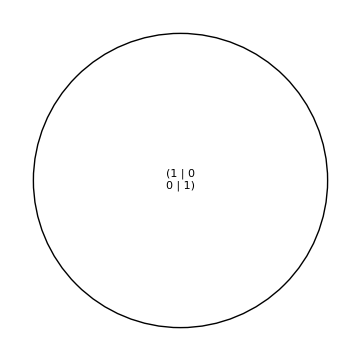

```mathematica
(* Caveat: Circle is invariant to rotational/mirroring transforms, which does not hold for other objects, which may point in oppposite directions (for mirroring transforms) *)
A = {{1,0},{0,1}}
%//MatrixForm
Graphics[{GeometricTransformation[Circle[],AffineTransform[{A,{0,0}}]],Inset[A,{0,0}]}]
```

{{1,0},{0,1.1}}

(1 | 0
0 | 1.1)

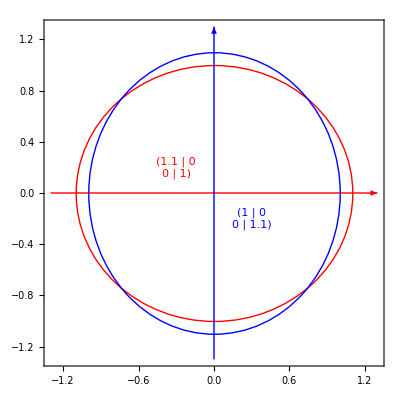

```mathematica
A = {{1.1,0},{0,1}};B={{1,0},{0,1.1}}
%//MatrixForm
Graphics[{Red,Arrow[{{-1.3,0},{1.3,0}}],GeometricTransformation[Circle[],AffineTransform[{A,{0,0}}]],Inset[A,{-0.3,0.2}],Blue,Arrow[{{0,-1.3},{0,1.3}}],GeometricTransformation[Circle[],AffineTransform[{B,{0,0}}]],Inset[B,{0.3,-0.2}]},Frame->True,PlotRange->{{-1.3,1.3},{-1.3,1.3}}]
```

```mathematica
Animate[Graphics[{GeometricTransformation[Circle[],AffineTransform[{{{a,0},{0,1}},{0,0}}]],Inset[{{a,0},{0,1}},{0,0}]}],{a,1.0,10},AnimationRunning->False]
```

```mathematica
SetDirectory@NotebookDirectory[]
Export["scale.swf",Table[Graphics[{GeometricTransformation[Circle[],AffineTransform[{{{a,0},{0,1}},{0,0}}]],Inset[{{a,0},{0,1}},{0,0}]}],{a,1.0,10,0.1}]]
```

C:\Users\sebi\Documents\studium_ainforimatik\master thesis

scale.swf

```mathematica
A={{2,0},{0,1}}
Det[A]
A={{Cos[a],Sin[a]},{-Sin[a],Cos[a]}}.{{2,0},{0,1}}
```

{{2,0},{0,1}}

2

{{2 Cos[a],Sin[a]},{-2 Sin[a],Cos[a]}}

```mathematica
Animate[Graphics[{GeometricTransformation[Circle[],AffineTransform[{{{2 Cos[a],Sin[a]},{-2 Sin[a],Cos[a]}},{0,0}}]],Inset[{{2 Cos[a],Sin[a]},{-2 Sin[a],Cos[a]}},{0,0}]}],{a,0.0,10,0.1},AnimationRunning->False]
```

```mathematica
Export["rotate.swf",Table[Graphics[{GeometricTransformation[Circle[],AffineTransform[{{{2 Cos[a],Sin[a]},{-2 Sin[a],Cos[a]}},{0,0}}]],Inset[{{2 Cos[a],Sin[a]},{-2 Sin[a],Cos[a]}},{0,0}]}],{a,0.0,10,0.1}]]
```

rotate.swf